# Space C*[a,b]

## Définition principale (Produit scalaire)

### Fonction poid

```mathematica
w:=1
```

### Intervalle d’orthogonalité

```mathematica
a:=-1
```

```mathematica
b:=1
```

### Produit scalaire

```mathematica
⟨f_|g_⟩:=∫_a^b w f* gⅆx
```

## Autres définitions

### La norme

```mathematica
norm[x_]:=√⟨x|x⟩
```

### Normalization d’un vecteur

```mathematica
normalize[x_]:=x/(√⟨x|x⟩)
```

### Normalization d’un ensemble de vecteur

```mathematica
normalizeListe[vectors_]:=Table[normalize[vectors[[i]]],{i,1,Length[vectors]}]
```

### La projection orthogonale de y sur x

```mathematica
projection[y_,x_]:=⟨x|y⟩x/⟨x|x⟩
```

### Orthogonalisation (Gram–Schmidt algorithm)

```mathematica
gramSchmidt[vectors_]:=Module[{oVectors=vectors},
Do[oVectors[[i]]-=projection[oVectors[[i]],oVectors[[j]]],{i,2,Length[vectors]},{j,1,i-1}];
oVectors]
```

### Matrice d’orthonormalité

```mathematica
orthogonality[vectors_]:=Table[⟨vectors[[i]]|vectors[[j]]⟩,{i,1,Length[vectors]},{j,1,Length[vectors]}]//Simplify//TableForm
```

## La base

### Base quelconque

La dimension de la base

```mathematica
dim:=7
```

```mathematica
baseQuelconque=Table[ⅇ^(ⅈ π n x),{n,0,dim-1}]
```

{1,ⅇ^(ⅈ π x),ⅇ^(2 ⅈ π x),ⅇ^(3 ⅈ π x),ⅇ^(4 ⅈ π x),ⅇ^(5 ⅈ π x),ⅇ^(6 ⅈ π x)}

```mathematica
(*baseQuelconque=Table[Sin[n π x] ,{n,1,dim}]*)
```

```mathematica
orthogonality[baseQuelconque]
```

2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2

### Base orthogonale

```mathematica
baseOrthogonale=gramSchmidt[baseQuelconque]
```

{1,ⅇ^(ⅈ π x),ⅇ^(2 ⅈ π x),ⅇ^(3 ⅈ π x),ⅇ^(4 ⅈ π x),ⅇ^(5 ⅈ π x),ⅇ^(6 ⅈ π x)}

```mathematica
orthogonality[baseOrthogonale]
```

2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2

### Base orthonormale

```mathematica
baseOrthonormale=normalizeListe[baseOrthogonale]//Simplify
```

{1/(√2),ⅇ^(ⅈ π x)/(√2),ⅇ^(2 ⅈ π x)/(√2),ⅇ^(3 ⅈ π x)/(√2),ⅇ^(4 ⅈ π x)/(√2),ⅇ^(5 ⅈ π x)/(√2),ⅇ^(6 ⅈ π x)/(√2)}

```mathematica
orthogonality[baseOrthonormale]
```

1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1

## Développement de F(x) sur une base

### La fonction à développer

```mathematica
F[x_] :=π ⅇ^(ⅈ π/2x)
```

### La base

```mathematica
u:=baseOrthonormale
```

### Les coéfficients

```mathematica
Subscript[c, n_]:=⟨u[[n]]|F[x] ⟩
```

```mathematica
Table[Subscript[c, n],{n,1,dim}]
```

{2 √2,2 √2,-(2 √2)/3,(2 √2)/5,-(2 √2)/7,(2 √2)/9,-(2 √2)/11}

### Développement

```mathematica
∑_(n=1)^dim Subscript[c, n] Subscript[𝓊, n]//Simplify
```

(2 √2 (3465 𝓊_1+3465 𝓊_2-1155 𝓊_3+693 𝓊_4-495 𝓊_5+385 𝓊_6-315 𝓊_7))/3465

```mathematica
Fdev[x_]=∑_(n=1)^dim Subscript[c, n] u[[n]]
```

2+2 ⅇ^(ⅈ π x)-2/3 ⅇ^(2 ⅈ π x)+2/5 ⅇ^(3 ⅈ π x)-2/7 ⅇ^(4 ⅈ π x)+2/9 ⅇ^(5 ⅈ π x)-2/11 ⅇ^(6 ⅈ π x)

### Représentation

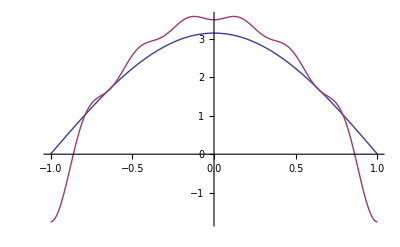

```mathematica
Plot[Evaluate[Re[{F[x],Fdev[x]}]],{x,a,b},PlotRange->All]
```

### Manipulation

```mathematica
Manipulate[Plot[Evaluate[Re[{F[x],∑_(n=1)^N Subscript[c, n] base[[n]]}]],{x,a,b},PlotRange->All],{N,1,dim,1},ControlType->Setter]
```